```mathematica
SetDirectory["L:/moose/trunk/wallaby/doc/theory/figures"]
```

L:\moose\trunk\wallaby\doc\theory\figures

```mathematica
k[s_] :=s^(1/2) (1 - (1 - s^(1/m))^m)^2;
seff[p_] := (1 + (p/1)^(1/(1-m)))^(-m); (* here set alpha=1 *)
pc[s_] := ( s^(-1/m) - 1)^(1-m);
kcos[s_] := (n+1)s^n - n s^(n+1);
```

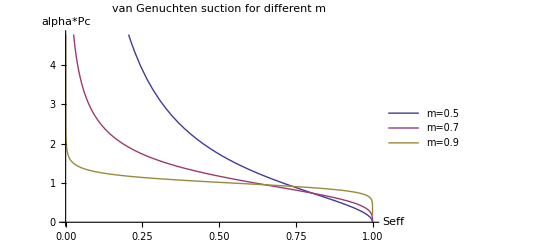

```mathematica
Plot[{pc[s]/.m->0.5,pc[s]/.m->0.7,pc[s]/.m->0.9},{s,0,1},PlotLegends->LineLegend[{"m=0.5","m=0.7","m=0.9"}],AxesLabel->{"Seff","alpha*Pc"},PlotLabel->"van Genuchten suction for different m"]
```

```mathematica
Export["van_genuchten_pc.eps",%]
```

van_genuchten_pc.eps

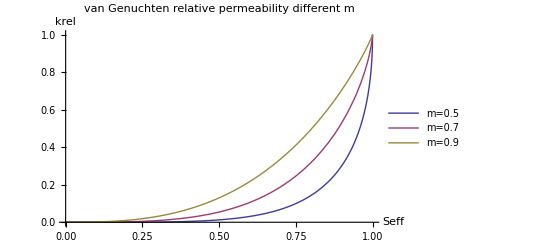

```mathematica
Plot[{k[s]/.m->0.5,k[s]/.m->0.7,k[s]/.m->0.9},{s,0,1},PlotLegends->LineLegend[{"m=0.5","m=0.7","m=0.9"}],AxesLabel->{"Seff","krel"},PlotLabel->"van Genuchten relative permeability different m"]
```

```mathematica
Export["van_genuchten_kr.eps",%]
```

van_genuchten_kr.eps

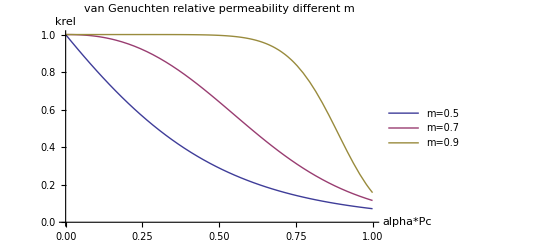

```mathematica
Plot[{k[seff[p]]/.m->0.5,k[seff[p]]/.m->0.7,k[seff[p]]/.m->0.9},{p,0,1},PlotLegends->LineLegend[{"m=0.5","m=0.7","m=0.9"}],AxesLabel->{"alpha*Pc","krel"},PlotLabel->"van Genuchten relative permeability different m"]
```

```mathematica
Export["van_genuchten_kr_pc.eps",%]
```

van_genuchten_kr_pc.eps

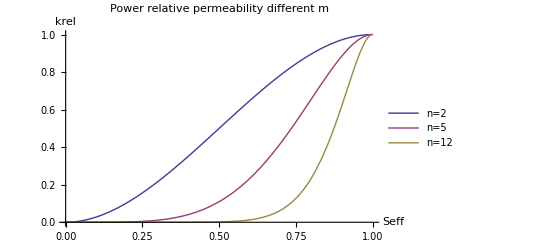

```mathematica
Plot[{kcos[s]/.n->2,kcos[s]/.n->5, kcos[s]/.n->12},{s,0,1},PlotLegends->LineLegend[{"n=2","n=5","n=12"}],AxesLabel->{"Seff","krel"},PlotLabel->"Power relative permeability different m"]
```

```mathematica
Export["power_kr.eps",%]
```

power_kr.eps

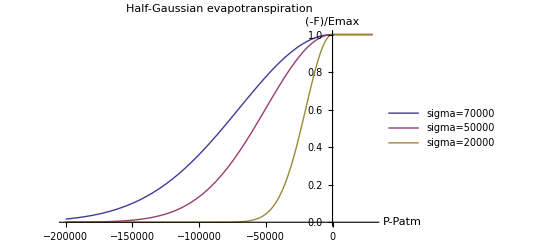

```mathematica
et[p_,si_] := If[p>0,1,Exp[-(1/2)*p^2/si^2]];
Plot[{et[p,7*10^4],et[p,5*10^4],et[p,2*10^4]},{p,-2*10^5,3*10^4},PlotRange->All,PlotLegends->LineLegend[{"sigma=70000", "sigma=50000", "sigma=20000"}],AxesLabel->{"P-Patm","(-F)/Emax"},PlotLabel->"Half-Gaussian evapotranspiration"]
```

```mathematica
Export["et.eps",%]
```

et.eps